# Runtime Testing

```mathematica
<<StoChemSim`
```

## Direct SSA

All system constructions have number of reactions = number of species.

```mathematica
(*System 1: Every species appears in precisely 1 reaction. Every reaction has only 1 reactant and 1 product.*)
ConstructSys1[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[x[i],y[i],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 2: Every species appears in O(sqrt(n)) reactions. Every reaction has O(sqrt(n)) reactants and O(sqrt(n)) products.*)
ConstructSys2[n_]:=Module[
{k,rxns,xConcs,yConcs,concs},
k=Round[Sqrt[n]];
rxns= Flatten[Table[revrxn[Plus@@Table[x[i,l]+x[j,l],{l,k}],Plus@@Table[y[i,l]+y[j,l],{l,k}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]];
xConcs=Flatten[Table[conc[x[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
yConcs=Flatten[Table[conc[y[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 3: Every species appears in all reactions. Every reaction has O(n) reactants and O(n) products.*)
ConstructSys3[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[Plus@@Table[x[j],{j,n}],Plus@@Table[y[j],{j,n}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
TestSysSSA[construction_,kRange_,iters_,statesOnlyFlag_]:=Module[{},
Table[Module[
{n,rxns,concs,rxnsys,nRxns,nSpecies,results,totalTime,runtimeInfo,totalTimePerIter,algoTimePerIter,out},
n=k^2;
{rxns,concs} = construction[n];
rxnsys=Flatten[{rxns,concs}];
nRxns=Length[ExpandRevrxns[rxns]];
nSpecies=Length[SpeciesInRxnsys[rxnsys]];
results=Timing[SimulateDirectSSA[rxnsys,useIter->True,iterEnd->iters,statesOnly->statesOnlyFlag,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
totalTimePerIter=totalTime/iters;
runtimeInfo=GetRuntimeInfo[];
out={construction,statesOnlyFlag,nRxns,nSpecies,iters,totalTime,totalTimePerIter,runtimeInfo};
Print[out];
out],
{k,kRange}]]
```

## Constructions 1, 2, and 3 up to 50 reactions

```mathematica
constructions={ConstructSys1,ConstructSys2,ConstructSys3};
kRange={1,3,5};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.203125,2.03125×10^-6,<|frontend→0.,interface→7.3×10^-6,backend→0.200916|>}

{ConstructSys1,False,18,18,100000,0.3125,3.125×10^-6,<|frontend→0.,interface→0.0000298,backend→0.320986|>}

{ConstructSys1,False,50,50,100000,0.546875,5.46875×10^-6,<|frontend→0.,interface→0.0000474,backend→0.534992|>}

{ConstructSys1,True,2,2,100000,0.203125,2.03125×10^-6,<|frontend→0.,interface→4.9×10^-6,backend→0.203739|>}

{ConstructSys1,True,18,18,100000,0.3125,3.125×10^-6,<|frontend→0.,interface→0.0000211,backend→0.308874|>}

{ConstructSys1,True,50,50,100000,0.546875,5.46875×10^-6,<|frontend→0.,interface→0.0000468,backend→0.536718|>}

{ConstructSys2,False,2,2,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→6.×10^-6,backend→0.225673|>}

{ConstructSys2,False,18,12,100000,1.23438,0.0000123438,<|frontend→0.,interface→0.000029,backend→1.2225|>}

{ConstructSys2,False,50,30,100000,3.625,0.00003625,<|frontend→0.015625,interface→0.0001321,backend→3.60926|>}

{ConstructSys2,True,2,2,100000,0.203125,2.03125×10^-6,<|frontend→0.,interface→4.8×10^-6,backend→0.199264|>}

{ConstructSys2,True,18,12,100000,1.26563,0.0000126563,<|frontend→0.,interface→0.0000359,backend→1.26868|>}

{ConstructSys2,True,50,30,100000,3.51563,0.0000351563,<|frontend→0.015625,interface→0.00008,backend→3.50771|>}

{ConstructSys3,False,2,2,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→8.1×10^-6,backend→0.222923|>}

{ConstructSys3,False,18,18,100000,5.48438,0.0000548438,<|frontend→0.015625,interface→0.0000927,backend→5.4751|>}

{ConstructSys3,False,50,50,100000,59.4219,0.000594219,<|frontend→0.015625,interface→0.0004879,backend→64.3362|>}

{ConstructSys3,True,2,2,100000,0.203125,2.03125×10^-6,<|frontend→0.,interface→9.5×10^-6,backend→0.240114|>}

{ConstructSys3,True,18,18,100000,6.25,0.0000625,<|frontend→0.,interface→0.0000902,backend→6.48992|>}

{ConstructSys3,True,50,50,100000,56.6563,0.000566563,<|frontend→0.03125,interface→0.0003274,backend→59.3089|>}

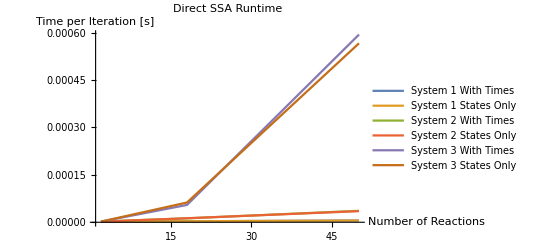

```mathematica
coorsSSA=Flatten[Table[
Table[{resultsSSA[[i]][[j]][[l]][[3]],resultsSSA[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2","System 3"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem], resultsSSA];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem], coorsSSA];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.203125,2.03125×10^-6,<|frontend→0.,interface→7.3×10^-6,backend→0.200916|>},{ConstructSys1,False,18,18,100000,0.3125,3.125×10^-6,<|frontend→0.,interface→0.0000298,backend→0.320986|>},{ConstructSys1,False,50,50,100000,0.546875,5.46875×10^-6,<|frontend→0.,interface→0.0000474,backend→0.534992|>}},{{ConstructSys1,True,2,2,100000,0.203125,2.03125×10^-6,<|frontend→0.,interface→4.9×10^-6,backend→0.203739|>},{ConstructSys1,True,18,18,100000,0.3125,3.125×10^-6,<|frontend→0.,interface→0.0000211,backend→0.308874|>},{ConstructSys1,True,50,50,100000,0.546875,5.46875×10^-6,<|frontend→0.,interface→0.0000468,backend→0.536718|>}}},{{{ConstructSys2,False,2,2,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→6.×10^-6,backend→0.225673|>},{ConstructSys2,False,18,12,100000,1.23438,0.0000123438,<|frontend→0.,interface→0.000029,backend→1.2225|>},{ConstructSys2,False,50,30,100000,3.625,0.00003625,<|frontend→0.015625,interface→0.0001321,backend→3.60926|>}},{{ConstructSys2,True,2,2,100000,0.203125,2.03125×10^-6,<|frontend→0.,interface→4.8×10^-6,backend→0.199264|>},{ConstructSys2,True,18,12,100000,1.26563,0.0000126563,<|frontend→0.,interface→0.0000359,backend→1.26868|>},{ConstructSys2,True,50,30,100000,3.51563,0.0000351563,<|frontend→0.015625,interface→0.00008,backend→3.50771|>}}},{{{ConstructSys3,False,2,2,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→8.1×10^-6,backend→0.222923|>},{ConstructSys3,False,18,18,100000,5.48438,0.0000548438,<|frontend→0.015625,interface→0.0000927,backend→5.4751|>},{ConstructSys3,False,50,50,100000,59.4219,0.000594219,<|frontend→0.015625,interface→0.0004879,backend→64.3362|>}},{{ConstructSys3,True,2,2,100000,0.203125,2.03125×10^-6,<|frontend→0.,interface→9.5×10^-6,backend→0.240114|>},{ConstructSys3,True,18,18,100000,6.25,0.0000625,<|frontend→0.,interface→0.0000902,backend→6.48992|>},{ConstructSys3,True,50,50,100000,56.6563,0.000566563,<|frontend→0.03125,interface→0.0003274,backend→59.3089|>}}}}

{{{2,2.03125×10^-6},{18,3.125×10^-6},{50,5.46875×10^-6}},{{2,2.03125×10^-6},{18,3.125×10^-6},{50,5.46875×10^-6}},{{2,2.1875×10^-6},{18,0.0000123438},{50,0.00003625}},{{2,2.03125×10^-6},{18,0.0000126563},{50,0.0000351563}},{{2,2.1875×10^-6},{18,0.0000548438},{50,0.000594219}},{{2,2.03125×10^-6},{18,0.0000625},{50,0.000566563}}}

## Constructions 1 and 2 up to 1,250 reactions

```mathematica
constructions={ConstructSys1,ConstructSys2};
kRange={1,3,5,10,25};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA2=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.21875,2.1875×10^-6,<|frontend→0.015625,interface→7.×10^-6,backend→0.208992|>}

{ConstructSys1,False,18,18,100000,0.328125,3.28125×10^-6,<|frontend→0.,interface→0.0000317,backend→0.317408|>}

{ConstructSys1,False,50,50,100000,0.546875,5.46875×10^-6,<|frontend→0.,interface→0.0001201,backend→0.540528|>}

{ConstructSys1,False,200,200,100000,1.95313,0.0000195313,<|frontend→0.03125,interface→0.0002974,backend→1.91199|>}

{ConstructSys1,False,1250,1250,100000,10.9219,0.000109219,<|frontend→0.453125,interface→0.0050459,backend→10.4734|>}

{ConstructSys1,True,2,2,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→8.3×10^-6,backend→0.217275|>}

{ConstructSys1,True,18,18,100000,0.34375,3.4375×10^-6,<|frontend→0.,interface→0.0000218,backend→0.340685|>}

{ConstructSys1,True,50,50,100000,0.5625,5.625×10^-6,<|frontend→0.,interface→0.0000464,backend→0.561525|>}

{ConstructSys1,True,200,200,100000,1.67188,0.0000167188,<|frontend→0.03125,interface→0.0002797,backend→1.65126|>}

{ConstructSys1,True,1250,1250,100000,9.82813,0.0000982813,<|frontend→0.375,interface→0.0027238,backend→9.54665|>}

{ConstructSys2,False,2,2,100000,0.265625,2.65625×10^-6,<|frontend→0.,interface→8.9×10^-6,backend→0.265328|>}

{ConstructSys2,False,18,12,100000,1.4375,0.000014375,<|frontend→0.015625,interface→0.0000294,backend→1.48209|>}

{ConstructSys2,False,50,30,100000,3.59375,0.0000359375,<|frontend→0.,interface→0.000129,backend→3.62057|>}

{ConstructSys2,False,200,110,100000,0.125,1.25×10^-6,<|frontend→0.0625,interface→0.0013258,backend→0.0402852|>}

{ConstructSys2,False,1250,650,100000,1.26563,0.0000126563,<|frontend→0.734375,interface→0.0079224,backend→0.509264|>}

{ConstructSys2,True,2,2,100000,0.25,2.5×10^-6,<|frontend→0.015625,interface→7.1×10^-6,backend→0.274315|>}

{ConstructSys2,True,18,12,100000,1.20313,0.0000120313,<|frontend→0.,interface→0.000031,backend→1.20858|>}

{ConstructSys2,True,50,30,100000,4.07813,0.0000407813,<|frontend→0.,interface→0.0001062,backend→4.07929|>}

{ConstructSys2,True,200,110,100000,0.109375,1.09375×10^-6,<|frontend→0.078125,interface→0.0006081,backend→0.043137|>}

{ConstructSys2,True,1250,650,100000,1.375,0.00001375,<|frontend→0.8125,interface→0.0097427,backend→0.545604|>}

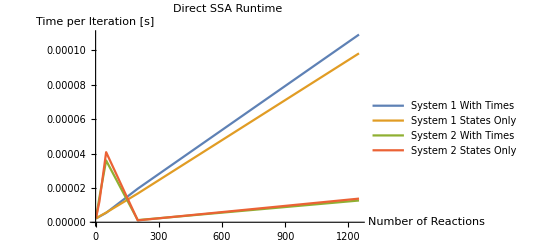

```mathematica
coorsSSA2=Flatten[Table[
Table[{resultsSSA2[[i]][[j]][[l]][[3]],resultsSSA2[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA2[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA2,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA2.mx"},OperatingSystem->$OperatingSystem], resultsSSA2];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA2.mx"},OperatingSystem->$OperatingSystem], coorsSSA2];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA2=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA2.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA2=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA2.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.21875,2.1875×10^-6,<|frontend→0.015625,interface→7.×10^-6,backend→0.208992|>},{ConstructSys1,False,18,18,100000,0.328125,3.28125×10^-6,<|frontend→0.,interface→0.0000317,backend→0.317408|>},{ConstructSys1,False,50,50,100000,0.546875,5.46875×10^-6,<|frontend→0.,interface→0.0001201,backend→0.540528|>},{ConstructSys1,False,200,200,100000,1.95313,0.0000195313,<|frontend→0.03125,interface→0.0002974,backend→1.91199|>},{ConstructSys1,False,1250,1250,100000,10.9219,0.000109219,<|frontend→0.453125,interface→0.0050459,backend→10.4734|>}},{{ConstructSys1,True,2,2,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→8.3×10^-6,backend→0.217275|>},{ConstructSys1,True,18,18,100000,0.34375,3.4375×10^-6,<|frontend→0.,interface→0.0000218,backend→0.340685|>},{ConstructSys1,True,50,50,100000,0.5625,5.625×10^-6,<|frontend→0.,interface→0.0000464,backend→0.561525|>},{ConstructSys1,True,200,200,100000,1.67188,0.0000167188,<|frontend→0.03125,interface→0.0002797,backend→1.65126|>},{ConstructSys1,True,1250,1250,100000,9.82813,0.0000982813,<|frontend→0.375,interface→0.0027238,backend→9.54665|>}}},{{{ConstructSys2,False,2,2,100000,0.265625,2.65625×10^-6,<|frontend→0.,interface→8.9×10^-6,backend→0.265328|>},{ConstructSys2,False,18,12,100000,1.4375,0.000014375,<|frontend→0.015625,interface→0.0000294,backend→1.48209|>},{ConstructSys2,False,50,30,100000,3.59375,0.0000359375,<|frontend→0.,interface→0.000129,backend→3.62057|>},{ConstructSys2,False,200,110,100000,0.125,1.25×10^-6,<|frontend→0.0625,interface→0.0013258,backend→0.0402852|>},{ConstructSys2,False,1250,650,100000,1.26563,0.0000126563,<|frontend→0.734375,interface→0.0079224,backend→0.509264|>}},{{ConstructSys2,True,2,2,100000,0.25,2.5×10^-6,<|frontend→0.015625,interface→7.1×10^-6,backend→0.274315|>},{ConstructSys2,True,18,12,100000,1.20313,0.0000120313,<|frontend→0.,interface→0.000031,backend→1.20858|>},{ConstructSys2,True,50,30,100000,4.07813,0.0000407813,<|frontend→0.,interface→0.0001062,backend→4.07929|>},{ConstructSys2,True,200,110,100000,0.109375,1.09375×10^-6,<|frontend→0.078125,interface→0.0006081,backend→0.043137|>},{ConstructSys2,True,1250,650,100000,1.375,0.00001375,<|frontend→0.8125,interface→0.0097427,backend→0.545604|>}}}}

{{{2,2.1875×10^-6},{18,3.28125×10^-6},{50,5.46875×10^-6},{200,0.0000195313},{1250,0.000109219}},{{2,2.1875×10^-6},{18,3.4375×10^-6},{50,5.625×10^-6},{200,0.0000167188},{1250,0.0000982813}},{{2,2.65625×10^-6},{18,0.000014375},{50,0.0000359375},{200,1.25×10^-6},{1250,0.0000126563}},{{2,2.5×10^-6},{18,0.0000120313},{50,0.0000407813},{200,1.09375×10^-6},{1250,0.00001375}}}

## Construction 1 up to 20,000 reactions

```mathematica
constructions={ConstructSys1};
kRange={1,3,5,10,25,50,100};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA3=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.234375,2.34375×10^-6,<|frontend→0.015625,interface→6.9×10^-6,backend→0.214886|>}

{ConstructSys1,False,18,18,100000,0.34375,3.4375×10^-6,<|frontend→0.,interface→0.0000293,backend→0.342639|>}

{ConstructSys1,False,50,50,100000,0.5625,5.625×10^-6,<|frontend→0.,interface→0.0000491,backend→0.557539|>}

{ConstructSys1,False,200,200,100000,1.64063,0.0000164063,<|frontend→0.015625,interface→0.0002759,backend→1.65762|>}

{ConstructSys1,False,1250,1250,100000,9.60938,0.0000960938,<|frontend→0.359375,interface→0.0030659,backend→9.34524|>}

{ConstructSys1,False,5000,5000,100000,53.6563,0.000536563,<|frontend→4.59375,interface→0.0441573,backend→50.3422|>}

{ConstructSys1,False,20000,20000,100000,296.25,0.0029625,<|frontend→77.7344,interface→1.19181,backend→219.684|>}

{ConstructSys1,True,2,2,100000,0.328125,3.28125×10^-6,<|frontend→0.015625,interface→0.0000116,backend→0.308713|>}

{ConstructSys1,True,18,18,100000,0.390625,3.90625×10^-6,<|frontend→0.,interface→0.0000425,backend→0.390681|>}

{ConstructSys1,True,50,50,100000,0.625,6.25×10^-6,<|frontend→0.,interface→0.0004507,backend→0.619551|>}

{ConstructSys1,True,200,200,100000,1.82813,0.0000182813,<|frontend→0.03125,interface→0.0003667,backend→1.81484|>}

{ConstructSys1,True,1250,1250,100000,10.3281,0.000103281,<|frontend→0.390625,interface→0.0051165,backend→10.018|>}

{ConstructSys1,True,5000,5000,100000,51.2344,0.000512344,<|frontend→4.76563,interface→0.042806,backend→46.6246|>}

{ConstructSys1,True,20000,20000,100000,302.422,0.00302422,<|frontend→71.9688,interface→1.30828,backend→233.771|>}

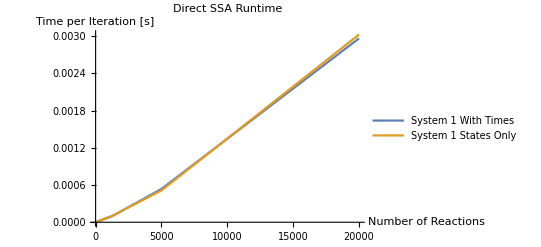

```mathematica
coorsSSA3=Flatten[Table[
Table[{resultsSSA3[[i]][[j]][[l]][[3]],resultsSSA3[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA3[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA3,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA3.mx"},OperatingSystem->$OperatingSystem], resultsSSA3];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA3.mx"},OperatingSystem->$OperatingSystem], coorsSSA3];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA3=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA3.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA3=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA3.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.234375,2.34375×10^-6,<|frontend→0.015625,interface→6.9×10^-6,backend→0.214886|>},{ConstructSys1,False,18,18,100000,0.34375,3.4375×10^-6,<|frontend→0.,interface→0.0000293,backend→0.342639|>},{ConstructSys1,False,50,50,100000,0.5625,5.625×10^-6,<|frontend→0.,interface→0.0000491,backend→0.557539|>},{ConstructSys1,False,200,200,100000,1.64063,0.0000164063,<|frontend→0.015625,interface→0.0002759,backend→1.65762|>},{ConstructSys1,False,1250,1250,100000,9.60938,0.0000960938,<|frontend→0.359375,interface→0.0030659,backend→9.34524|>},{ConstructSys1,False,5000,5000,100000,53.6563,0.000536563,<|frontend→4.59375,interface→0.0441573,backend→50.3422|>},{ConstructSys1,False,20000,20000,100000,296.25,0.0029625,<|frontend→77.7344,interface→1.19181,backend→219.684|>}},{{ConstructSys1,True,2,2,100000,0.328125,3.28125×10^-6,<|frontend→0.015625,interface→0.0000116,backend→0.308713|>},{ConstructSys1,True,18,18,100000,0.390625,3.90625×10^-6,<|frontend→0.,interface→0.0000425,backend→0.390681|>},{ConstructSys1,True,50,50,100000,0.625,6.25×10^-6,<|frontend→0.,interface→0.0004507,backend→0.619551|>},{ConstructSys1,True,200,200,100000,1.82813,0.0000182813,<|frontend→0.03125,interface→0.0003667,backend→1.81484|>},{ConstructSys1,True,1250,1250,100000,10.3281,0.000103281,<|frontend→0.390625,interface→0.0051165,backend→10.018|>},{ConstructSys1,True,5000,5000,100000,51.2344,0.000512344,<|frontend→4.76563,interface→0.042806,backend→46.6246|>},{ConstructSys1,True,20000,20000,100000,302.422,0.00302422,<|frontend→71.9688,interface→1.30828,backend→233.771|>}}}}

{{{2,2.34375×10^-6},{18,3.4375×10^-6},{50,5.625×10^-6},{200,0.0000164063},{1250,0.0000960938},{5000,0.000536563},{20000,0.0029625}},{{2,3.28125×10^-6},{18,3.90625×10^-6},{50,6.25×10^-6},{200,0.0000182813},{1250,0.000103281},{5000,0.000512344},{20000,0.00302422}}}

## Bounded Tau Leaping

```mathematica
<<StoChemSim`
```

```mathematica
ConstructSysMax[n_]:={
rxnl[{x1},{y,z1},1],
rxnl[{x2},{y,z2},1],
rxnl[{z1,z2},{k},1/n],
rxnl[{k,y},{},1/n],
conc[{x1,x2},n/2]
};
```

```mathematica
TestSysBTL[construction_,simulation_,nRange_]:=Module[{},
Table[Module[
{rxnsys,results,totalTime,runtimeInfo,algoTime},
rxnsys= construction[n];
results=Timing[simulation[rxnsys,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
runtimeInfo=GetRuntimeInfo[];
out={simulation,n,totalTime,runtimeInfo};
Print[out];
out],
{n,nRange}]]
```

## Direct SSA vs. BTL up to 32,768 molecules

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[2^i,{i,1,15}];
resultsBTL=Table[TestSysBTL[ConstructSysMax,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,2,0.015625,<|frontend→0.,interface→0.0000108,backend→0.0000403|>}

{SimulateDirectSSA,4,0.,<|frontend→0.,interface→4.5×10^-6,backend→0.0000403|>}

{SimulateDirectSSA,8,0.,<|frontend→0.,interface→4.6×10^-6,backend→0.000056|>}

{SimulateDirectSSA,16,0.,<|frontend→0.,interface→4.6×10^-6,backend→0.0000941|>}

{SimulateDirectSSA,32,0.,<|frontend→0.,interface→5.×10^-6,backend→0.000498|>}

{SimulateDirectSSA,64,0.,<|frontend→0.,interface→5.1×10^-6,backend→0.0004491|>}

{SimulateDirectSSA,128,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.0006118|>}

{SimulateDirectSSA,256,0.,<|frontend→0.,interface→5.2×10^-6,backend→0.0011198|>}

{SimulateDirectSSA,512,0.,<|frontend→0.,interface→8.9×10^-6,backend→0.0024774|>}

{SimulateDirectSSA,1024,0.015625,<|frontend→0.,interface→6.2×10^-6,backend→0.0098034|>}

{SimulateDirectSSA,2048,0.015625,<|frontend→0.,interface→0.0000125,backend→0.0114198|>}

{SimulateDirectSSA,4096,0.015625,<|frontend→0.,interface→7.7×10^-6,backend→0.0237855|>}

{SimulateDirectSSA,8192,0.0625,<|frontend→0.,interface→0.0000164,backend→0.0567193|>}

{SimulateDirectSSA,16384,0.09375,<|frontend→0.,interface→0.0000104,backend→0.097513|>}

{SimulateDirectSSA,32768,0.15625,<|frontend→0.,interface→9.9×10^-6,backend→0.162193|>}

{SimulateBoundedTauLeaping,2,0.,<|frontend→0.,interface→7.1×10^-6,backend→0.0000621|>}

{SimulateBoundedTauLeaping,4,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0001156|>}

{SimulateBoundedTauLeaping,8,0.,<|frontend→0.,interface→6.4×10^-6,backend→0.0002163|>}

{SimulateBoundedTauLeaping,16,0.,<|frontend→0.,interface→5.9×10^-6,backend→0.0004169|>}

{SimulateBoundedTauLeaping,32,0.,<|frontend→0.,interface→9.4×10^-6,backend→0.0008653|>}

{SimulateBoundedTauLeaping,64,0.,<|frontend→0.,interface→8.6×10^-6,backend→0.0017063|>}

{SimulateBoundedTauLeaping,128,0.,<|frontend→0.,interface→8.1×10^-6,backend→0.0034942|>}

{SimulateBoundedTauLeaping,256,0.015625,<|frontend→0.015625,interface→0.0000172,backend→0.0082591|>}

{SimulateBoundedTauLeaping,512,0.015625,<|frontend→0.,interface→9.2×10^-6,backend→0.0126055|>}

{SimulateBoundedTauLeaping,1024,0.015625,<|frontend→0.,interface→0.0000129,backend→0.0162094|>}

{SimulateBoundedTauLeaping,2048,0.03125,<|frontend→0.,interface→9.×10^-6,backend→0.0255873|>}

{SimulateBoundedTauLeaping,4096,0.03125,<|frontend→0.,interface→0.0000112,backend→0.0284978|>}

{SimulateBoundedTauLeaping,8192,0.03125,<|frontend→0.,interface→7.3×10^-6,backend→0.0376753|>}

{SimulateBoundedTauLeaping,16384,0.03125,<|frontend→0.,interface→7.5×10^-6,backend→0.0561504|>}

{SimulateBoundedTauLeaping,32768,0.0625,<|frontend→0.,interface→8.8×10^-6,backend→0.0685291|>}

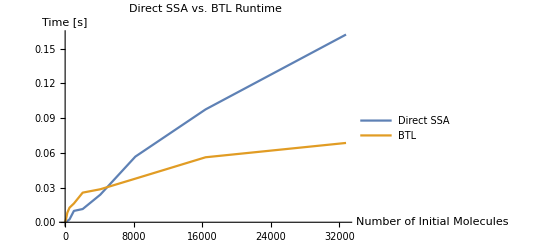

```mathematica
coorsBTL=Table[
Table[{resultsBTL[[i]][[l]][[2]],resultsBTL[[i]][[l]][[4]]["backend"]},{l,Length[resultsBTL[[i]]]}],
{i,Length[simulations]}];
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem], resultsBTL];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem], coorsBTL];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,2,0.015625,<|frontend→0.,interface→0.0000108,backend→0.0000403|>},{SimulateDirectSSA,4,0.,<|frontend→0.,interface→4.5×10^-6,backend→0.0000403|>},{SimulateDirectSSA,8,0.,<|frontend→0.,interface→4.6×10^-6,backend→0.000056|>},{SimulateDirectSSA,16,0.,<|frontend→0.,interface→4.6×10^-6,backend→0.0000941|>},{SimulateDirectSSA,32,0.,<|frontend→0.,interface→5.×10^-6,backend→0.000498|>},{SimulateDirectSSA,64,0.,<|frontend→0.,interface→5.1×10^-6,backend→0.0004491|>},{SimulateDirectSSA,128,0.,<|frontend→0.,interface→5.5×10^-6,backend→0.0006118|>},{SimulateDirectSSA,256,0.,<|frontend→0.,interface→5.2×10^-6,backend→0.0011198|>},{SimulateDirectSSA,512,0.,<|frontend→0.,interface→8.9×10^-6,backend→0.0024774|>},{SimulateDirectSSA,1024,0.015625,<|frontend→0.,interface→6.2×10^-6,backend→0.0098034|>},{SimulateDirectSSA,2048,0.015625,<|frontend→0.,interface→0.0000125,backend→0.0114198|>},{SimulateDirectSSA,4096,0.015625,<|frontend→0.,interface→7.7×10^-6,backend→0.0237855|>},{SimulateDirectSSA,8192,0.0625,<|frontend→0.,interface→0.0000164,backend→0.0567193|>},{SimulateDirectSSA,16384,0.09375,<|frontend→0.,interface→0.0000104,backend→0.097513|>},{SimulateDirectSSA,32768,0.15625,<|frontend→0.,interface→9.9×10^-6,backend→0.162193|>}},{{SimulateBoundedTauLeaping,2,0.,<|frontend→0.,interface→7.1×10^-6,backend→0.0000621|>},{SimulateBoundedTauLeaping,4,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0001156|>},{SimulateBoundedTauLeaping,8,0.,<|frontend→0.,interface→6.4×10^-6,backend→0.0002163|>},{SimulateBoundedTauLeaping,16,0.,<|frontend→0.,interface→5.9×10^-6,backend→0.0004169|>},{SimulateBoundedTauLeaping,32,0.,<|frontend→0.,interface→9.4×10^-6,backend→0.0008653|>},{SimulateBoundedTauLeaping,64,0.,<|frontend→0.,interface→8.6×10^-6,backend→0.0017063|>},{SimulateBoundedTauLeaping,128,0.,<|frontend→0.,interface→8.1×10^-6,backend→0.0034942|>},{SimulateBoundedTauLeaping,256,0.015625,<|frontend→0.015625,interface→0.0000172,backend→0.0082591|>},{SimulateBoundedTauLeaping,512,0.015625,<|frontend→0.,interface→9.2×10^-6,backend→0.0126055|>},{SimulateBoundedTauLeaping,1024,0.015625,<|frontend→0.,interface→0.0000129,backend→0.0162094|>},{SimulateBoundedTauLeaping,2048,0.03125,<|frontend→0.,interface→9.×10^-6,backend→0.0255873|>},{SimulateBoundedTauLeaping,4096,0.03125,<|frontend→0.,interface→0.0000112,backend→0.0284978|>},{SimulateBoundedTauLeaping,8192,0.03125,<|frontend→0.,interface→7.3×10^-6,backend→0.0376753|>},{SimulateBoundedTauLeaping,16384,0.03125,<|frontend→0.,interface→7.5×10^-6,backend→0.0561504|>},{SimulateBoundedTauLeaping,32768,0.0625,<|frontend→0.,interface→8.8×10^-6,backend→0.0685291|>}}}

{{{2,0.0000403},{4,0.0000403},{8,0.000056},{16,0.0000941},{32,0.000498},{64,0.0004491},{128,0.0006118},{256,0.0011198},{512,0.0024774},{1024,0.0098034},{2048,0.0114198},{4096,0.0237855},{8192,0.0567193},{16384,0.097513},{32768,0.162193}},{{2,0.0000621},{4,0.0001156},{8,0.0002163},{16,0.0004169},{32,0.0008653},{64,0.0017063},{128,0.0034942},{256,0.0082591},{512,0.0126055},{1024,0.0162094},{2048,0.0255873},{4096,0.0284978},{8192,0.0376753},{16384,0.0561504},{32768,0.0685291}}}

## Direct SSA vs. BTL up to 1,000,000 molecules

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[10^i,{i,1,6}];
resultsBTL2=Table[TestSysBTL[ConstructSysMax,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,10,0.,<|frontend→0.,interface→0.0000128,backend→0.000256|>}

{SimulateDirectSSA,100,0.,<|frontend→0.,interface→6.×10^-6,backend→0.0004678|>}

{SimulateDirectSSA,1000,0.015625,<|frontend→0.,interface→5.6×10^-6,backend→0.0053296|>}

{SimulateDirectSSA,10000,0.046875,<|frontend→0.,interface→7.2×10^-6,backend→0.0557686|>}

{SimulateDirectSSA,100000,0.46875,<|frontend→0.,interface→8.×10^-6,backend→0.48|>}

{SimulateDirectSSA,1000000,4.6875,<|frontend→0.,interface→6.9×10^-6,backend→4.72336|>}

{SimulateBoundedTauLeaping,10,0.015625,<|frontend→0.,interface→0.0000146,backend→0.0004143|>}

{SimulateBoundedTauLeaping,100,0.,<|frontend→0.,interface→9.6×10^-6,backend→0.0052178|>}

{SimulateBoundedTauLeaping,1000,0.03125,<|frontend→0.,interface→0.0000227,backend→0.0221199|>}

{SimulateBoundedTauLeaping,10000,0.046875,<|frontend→0.,interface→0.0000118,backend→0.059873|>}

{SimulateBoundedTauLeaping,100000,0.203125,<|frontend→0.015625,interface→0.0000148,backend→0.235834|>}

{SimulateBoundedTauLeaping,1000000,0.21875,<|frontend→0.,interface→0.0000127,backend→0.364766|>}

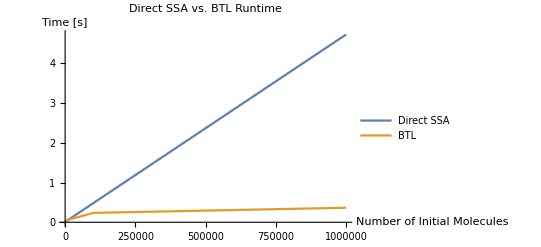

```mathematica
coorsBTL2=Table[
Table[{resultsBTL2[[i]][[l]][[2]],resultsBTL2[[i]][[l]][[4]]["backend"]},{l,Length[resultsBTL2[[i]]]}],
{i,Length[simulations]}];
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL2,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL2.mx"},OperatingSystem->$OperatingSystem], resultsBTL2];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL2.mx"},OperatingSystem->$OperatingSystem], coorsBTL2];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL2=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL2.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL2=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL2.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,10,0.,<|frontend→0.,interface→0.0000128,backend→0.000256|>},{SimulateDirectSSA,100,0.,<|frontend→0.,interface→6.×10^-6,backend→0.0004678|>},{SimulateDirectSSA,1000,0.015625,<|frontend→0.,interface→5.6×10^-6,backend→0.0053296|>},{SimulateDirectSSA,10000,0.046875,<|frontend→0.,interface→7.2×10^-6,backend→0.0557686|>},{SimulateDirectSSA,100000,0.46875,<|frontend→0.,interface→8.×10^-6,backend→0.48|>},{SimulateDirectSSA,1000000,4.6875,<|frontend→0.,interface→6.9×10^-6,backend→4.72336|>}},{{SimulateBoundedTauLeaping,10,0.015625,<|frontend→0.,interface→0.0000146,backend→0.0004143|>},{SimulateBoundedTauLeaping,100,0.,<|frontend→0.,interface→9.6×10^-6,backend→0.0052178|>},{SimulateBoundedTauLeaping,1000,0.03125,<|frontend→0.,interface→0.0000227,backend→0.0221199|>},{SimulateBoundedTauLeaping,10000,0.046875,<|frontend→0.,interface→0.0000118,backend→0.059873|>},{SimulateBoundedTauLeaping,100000,0.203125,<|frontend→0.015625,interface→0.0000148,backend→0.235834|>},{SimulateBoundedTauLeaping,1000000,0.21875,<|frontend→0.,interface→0.0000127,backend→0.364766|>}}}

{{{10,0.000256},{100,0.0004678},{1000,0.0053296},{10000,0.0557686},{100000,0.48},{1000000,4.72336}},{{10,0.0004143},{100,0.0052178},{1000,0.0221199},{10000,0.059873},{100000,0.235834},{1000000,0.364766}}}